```mathematica
s=DSolve[{y'[x]==-10^5/x^2(y[x]^2-(Integrate[u^2/Exp[√(u^2+x^2)],{u,0,Infinity}]/2)^2),y[0]==1},y,{x,0,100}]
```

```mathematica
LogLogPlot[Evaluate[y[x]/. s],{x,1,100}]
```

```mathematica
K=Integrate[((m^2+2 p^2 u)/(2 p^2 u^2))^2 Exp[-(m^2+2 p^2 u)/(2T p u)],{u,0,2}]
```

ConditionalExpression[(ⅇ^(-(m^2+4 p^2)/(4 p T)) T (m^4+8 m^2 p (p+T)+16 p^2 (p^2+2 p T+2 T^2)))/(8 m^2 p^3), Re[m^2/(p T)]≥0]

```mathematica
F[p_]:=ⅇ^(-(m^2+4 p^2)/(4 p T)) (p^2+2 p T+2 T^2)
Integrate[F[p],{p,0,Infinity}]
```

ConditionalExpression[(√T (m^2+8 T^2) BesselK[1,1/(√T √(T/m^2))])/(4 √(T/m^2))+2 m^2 T BesselK[2,1/(√T √(T/m^2))], Re[m^2/T]≥0&&Re[T]>0]

```mathematica
Series[BesselK[1,m/T],{m,0,1}]
```

(T/m+((2 log(m)+2 log(1/(2 T))+2 ℽ-1) m)/(4 T)+O(m^2))+((ⅈ π m)/T+O(m^2)) Floor[(-arg(m)-arg(1/T)+π)/(2 π)]

```mathematica
Series[BesselK[1,m/T],{m,Infinity,1}]
```

((√(π/2) √(1/m))/(√(1/T))+O((1/m)^(3/2))) exp(-m/T+O((1/m)^2))

```mathematica
Subscript[n, s]=(Subscript[g, s] 4Pi)/(2Pi)^3 Integrate[ e √(e^2-m^2) Exp[-e/T],{e,m,Infinity},Assumptions->{m>0,T>0}]
```

(m^2 T BesselK[2,m/T] g_s)/(2 π^2)

(m^2 T g_s)/(π^2 x^2)-(m^2 T g_s)/(4 π^2)+O[x]^2

ⅇ^(-x+O[1/x]^2) ((m^2 T g_s √(1/x))/(2 √2 π^(3/2))+O[1/x]^(3/2))

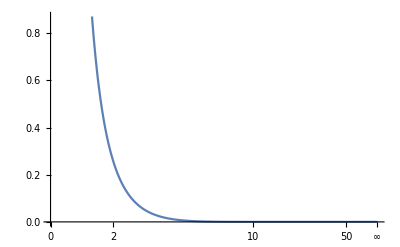

```mathematica
Subscript[n, UR]=(m^2 T  Subscript[g, s])/(2 π^2)Series[BesselK[2,x],{x,0,1}]
Subscript[n, NR]=(m^2 T  Subscript[g, s])/(2 π^2)Series[BesselK[2,x],{x,Infinity,1}]
Plot[BesselK[2,x],{x,0,Infinity}]
```

```mathematica
Subscript[n, UR]=(T^3 Subscript[g, s])/π^2
Subscript[n, NR]= Subscript[g, s] (mT/(2π))^(3/2)Exp[-m/T]
```

```mathematica
Integrate[Exp[-u/T],{u,m^2/(4p),Infinity}]
```

ConditionalExpression[ⅇ^(-m^2/(4 p T)) T, Re[T]>0]

```mathematica
Integrate[ⅇ^(-m^2/(4 p T))Exp[-p/T]T,{p,0,Infinity}]
```

ConditionalExpression[(T^(3/2) BesselK[1,1/(√T √(T/m^2))])/(√(T/m^2)), Re[m^2/T]>0&&Re[T]>0]

```mathematica
T m BesselK[1,m/T]
```

m T BesselK[1,m/T]

```mathematica
II=Pi^2/(2Pi)^5 T m BesselK[1,m/T]
Lambda=II 4/3 α^2 m^2 /(2 T^3/Pi^2)
NRatiao=(2 T^3)/Pi^2/((3 m^2 T)/(2 Pi^2)BesselK[2,m/T])
```

(m T BesselK[1,m/T])/(32 π^3)

(m^3 α^2 BesselK[1,m/T])/(48 π T^2)

(4 T^2)/(3 m^2 BesselK[2,m/T])

接下来计算 H (x = 1)

```mathematica
x=m/T
H~√Subscript[g, s] m^2
```

```mathematica
Q=1.293MeV; Subscript[g, s0]=10.75
```

```mathematica
H=1.13 √(3.5/10.75)(100/1.293)^2
```

```mathematica
10^-22/(48Pi H)
```

1.71948×10^-28